# White-Bear-Mark II Functional

The White-Bear mark II functional  is obtained using a more accurate equation of state for hard-sphere mixtures.
It takes the form

```mathematica
ϕ1[n3_]:=1+(2*n3-n3^2+2*(1-n3)*Log[1-n3])/(3*n3)
ϕ2[n3_]:=1-(2*n3-3*n3^2+2*n3^3+2*(1-n3)^2*Log[1-n3])/(3*n3^2)
phi[n0_,n1_,n2_,n3_,n1v_,n2v_,nt1_,nt2_]:=-n0*Log[1-n3] + ϕ1[n3]*(n1*n2-n1v*n2v)/(1-n3) + ϕ2[n3]*(n2^3-3*n2*n2v^2)/(24*Pi*(1-n3)^2)
f =η*(Log[C*η]-1)+Pi/6*σ^3*phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0}//Simplify
```

(η (-1+6 η-4 η^2+(-1+η)^2 Log[C η]))/(-1+η)^2

```mathematica
p = -f + η*D[f,η]//Simplify
mu = D[f-η*(Log[C*η]-1),η]//Simplify
z =Pi/6*σ^3/η*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0}//Simplify 
γ = Pi*σ^2*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0}//Simplify
χ = (η*D[mu+Log[η],η])^(-1)//Simplify
```

(η (-1-η-η^2+η^3))/(-1+η)^3

(η (-8+9 η-3 η^2))/(-1+η)^3

-(1+η+η^2-η^3)/(-1+η)^3

(η (2+3 η-2 η^2))/(-1+η)^2-Log[1-η]

(-1+η)^4/(1+4 η+4 η^2-4 η^3+η^4)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n0]//Simplify
```

-Log[1-n3]

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1]//Simplify
```

1/3 n2 ((-5+n3)/(-1+n3)+(2 Log[1-n3])/n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]//Simplify
```

(n3 (-n2^2 (1-3 n3+n3^2)+n2v^2 (1-3 n3+n3^2)+4 n1 n3 (5-6 n3+n3^2) π)+(-1+n3)^2 (-n2^2+n2v^2+8 n1 n3 π) Log[1-n3])/(12 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]//Simplify
```

1/(36 (-1+n3)^3 n3^3 π)(n3 (n2^3 (-2+5 n3-6 n3^2+n3^3)-12 (-1+n3) n3 (3 n0 (-1+n3) n3+2 n1v n2v (-1+3 n3)) π-3 n2 (n2v^2 (-2+5 n3-6 n3^2+n3^3)-8 n1 n3 (1-4 n3+3 n3^2) π))+2 (-1+n3)^3 (n2^3+12 n1v n2v n3 π-3 n2 (n2v^2+4 n1 n3 π)) Log[1-n3])

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1v]//Simplify
```

1/3 n2v ((5-n3)/(-1+n3)-(2 Log[1-n3])/n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2v]//Simplify
```

(n3 (n2 n2v (1-3 n3+n3^2)-2 n1v n3 (5-6 n3+n3^2) π)+(-1+n3)^2 (n2 n2v-4 n1v n3 π) Log[1-n3])/(6 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt1]//Simplify
```

0

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt2]//Simplify
```

0

```mathematica
D[ϕ1[n3]/(1-n3),n3]//Simplify
```

-(2 (n3-3 n3^2+(-1+n3)^2 Log[1-n3]))/(3 (-1+n3)^2 n3^2)

```mathematica
D[ϕ2[n3]/(24*Pi*(1-n3)^2),n3]//Simplify
```

(n3 (-2+5 n3-6 n3^2+n3^3)+2 (-1+n3)^3 Log[1-n3])/(36 (-1+n3)^3 n3^3 π)

```mathematica
Series[ϕ1[n3],{n3,0,2}]
```

1+n3^2/9+O[n3]^3

```mathematica
Series[ϕ2[n3],{n3,0,2}]
```

1-(4 n3)/9+n3^2/18+O[n3]^3

```mathematica
Series[D[ϕ1[n3]/(1-n3),n3],{n3,0,2}]
```

1+(20 n3)/9+(7 n3^2)/2+O[n3]^3

```mathematica
Series[D[ϕ2[n3]/(24*Pi*(1-n3)^2),n3],{n3,0,2}]
```

7/(108 π)+(13 n3)/(72 π)+(7 n3^2)/(20 π)+O[n3]^3

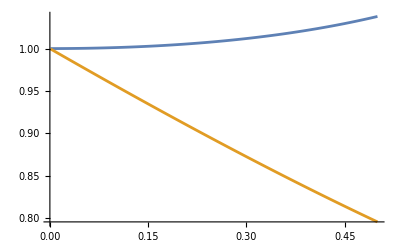

```mathematica
Plot[{ϕ1[x],ϕ2[x]},{x,0.001,0.5}]
```